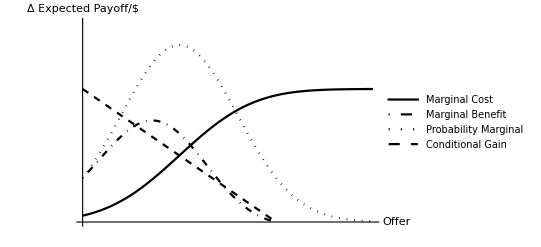

```mathematica
condMeanP[signal_,sRp_,rhoSeP_,meanP_]:=meanP+sRp *rhoSeP*signal
condSigP[sRp_,rhoSeP_]:=sRp*Sqrt[1-rhoSeP^2]
alpha[rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=sEnv*(rhoEnvRp-rhoES*rhoSeP)/(sRp*(1-rhoSeP^2))
a[meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=meanE+rhoES*sEnv*signal-alpha[rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]*condMeanP[signal,sRp,rhoSeP,meanP]
pA[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=CDF[NormalDistribution[condMeanP[signal,sRp,rhoSeP,meanP],condSigP[sRp,rhoSeP]],x]
pM[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=PDF[NormalDistribution[condMeanP[signal,sRp,rhoSeP,meanP],condSigP[sRp,rhoSeP]],x]
condGain[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=a[meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]-(1-alpha[rhoES,sEnv,sRp,rhoEnvRp,rhoSeP])*x
MB[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=pM[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]*condGain[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]
rpf[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=pA[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]*(meanE+rhoES*sEnv*signal-x)-sEnv*sRp*(rhoEnvRp-rhoES*rhoSeP)*pM[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]
drpf[x_,meanE_,meanP_,signal_,rhoES_,sEnv_,sRp_,rhoEnvRp_,rhoSeP_]:=MB[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]-pA[x,meanE,meanP,signal,rhoES,sEnv,sRp,rhoEnvRp,rhoSeP]
baseMeanE = 1; baseMeanP=.5; baseSEnv=1.5; baseSrp = .3; baseRhoES=.5; baseRhoSeP=0;xMax =1.5;yRange={0,1.5};
plotStyleList = {Red,{Red,Dotted},{Red,Dashed},Blue,{Blue,Dotted},{Blue,Dashed}};
plotStyleList = {Red,Blue};
sigZVals = {-.5,0,.5}; rhoVals ={-.5,0,.5}; 
baseMBvMCplot=Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoVals[[2]],baseRhoSeP]},
{x,0,xMax},PlotStyle->{Black,{Black,DotDashed},{Black,Dotted},{Black,Dashed}},PlotRange->yRange,Ticks->None,PlotLegends->{"Marginal Cost","Marginal Benefit","Probability Marginal","Conditional Gain"},AxesLabel->{ "Offer","Δ Expected Payoff/$"}]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\baseMBvMC.eps",baseMBvMCplot,"EPS"];
```

## MB/MC Grid

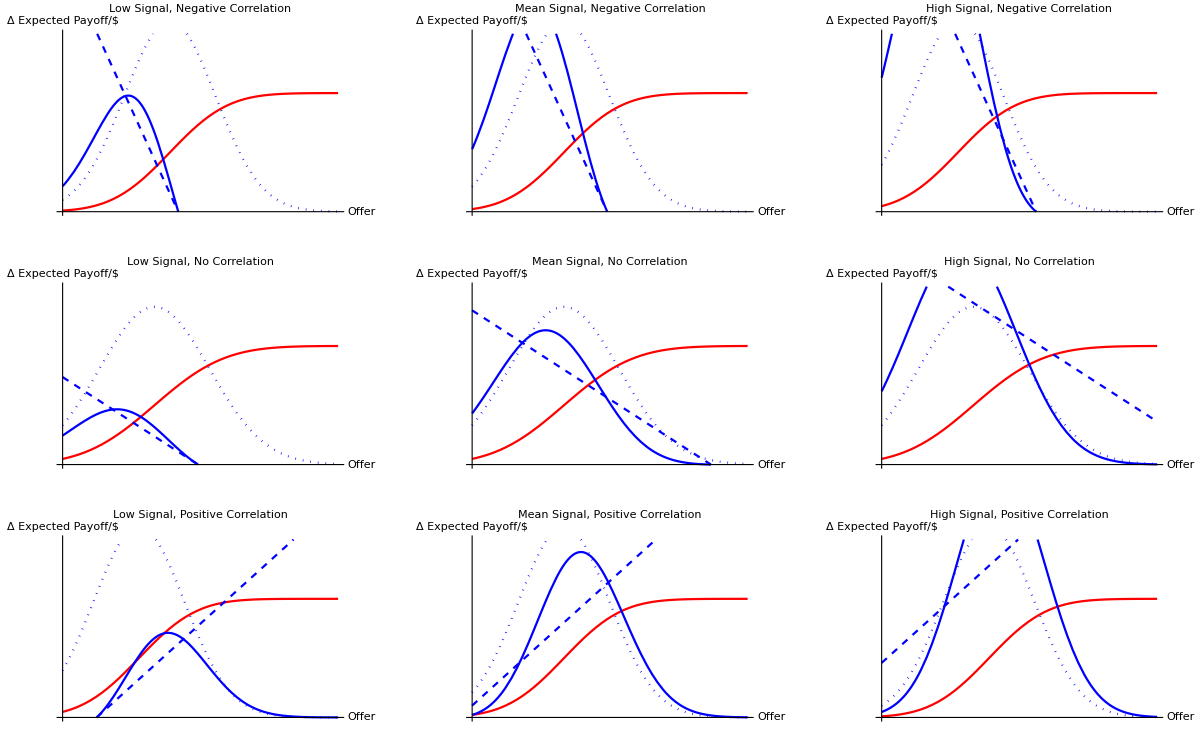

```mathematica
baseRhoES = .75;baseSEnv = 1.5; baseMeanE = 1.3;rhoEPVals = {-.75,0,.75}; rhoSPVals=rhoEPVals*baseRhoES;plotStyleList={Red,Blue,{Blue,Dotted},{Blue,Dashed}}; yRange={0,1.5}; 
plotOptions = {PlotStyle->plotStyleList,PlotRange->yRange,Ticks->None,AxesLabel->{"Offer","Δ Expected Payoff/$"}};
GraphicsGrid[{
{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, Negative Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, Negative Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, Negative Correlation"]},

{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, No Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, No Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, No Correlation"]},

{Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Low Signal, Positive Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"Mean Signal, Positive Correlation"],
Plot[{pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptions,PlotLabel->"High Signal, Positive Correlation"]}}
,ImageSize->Full]
```

## Marginal Cost

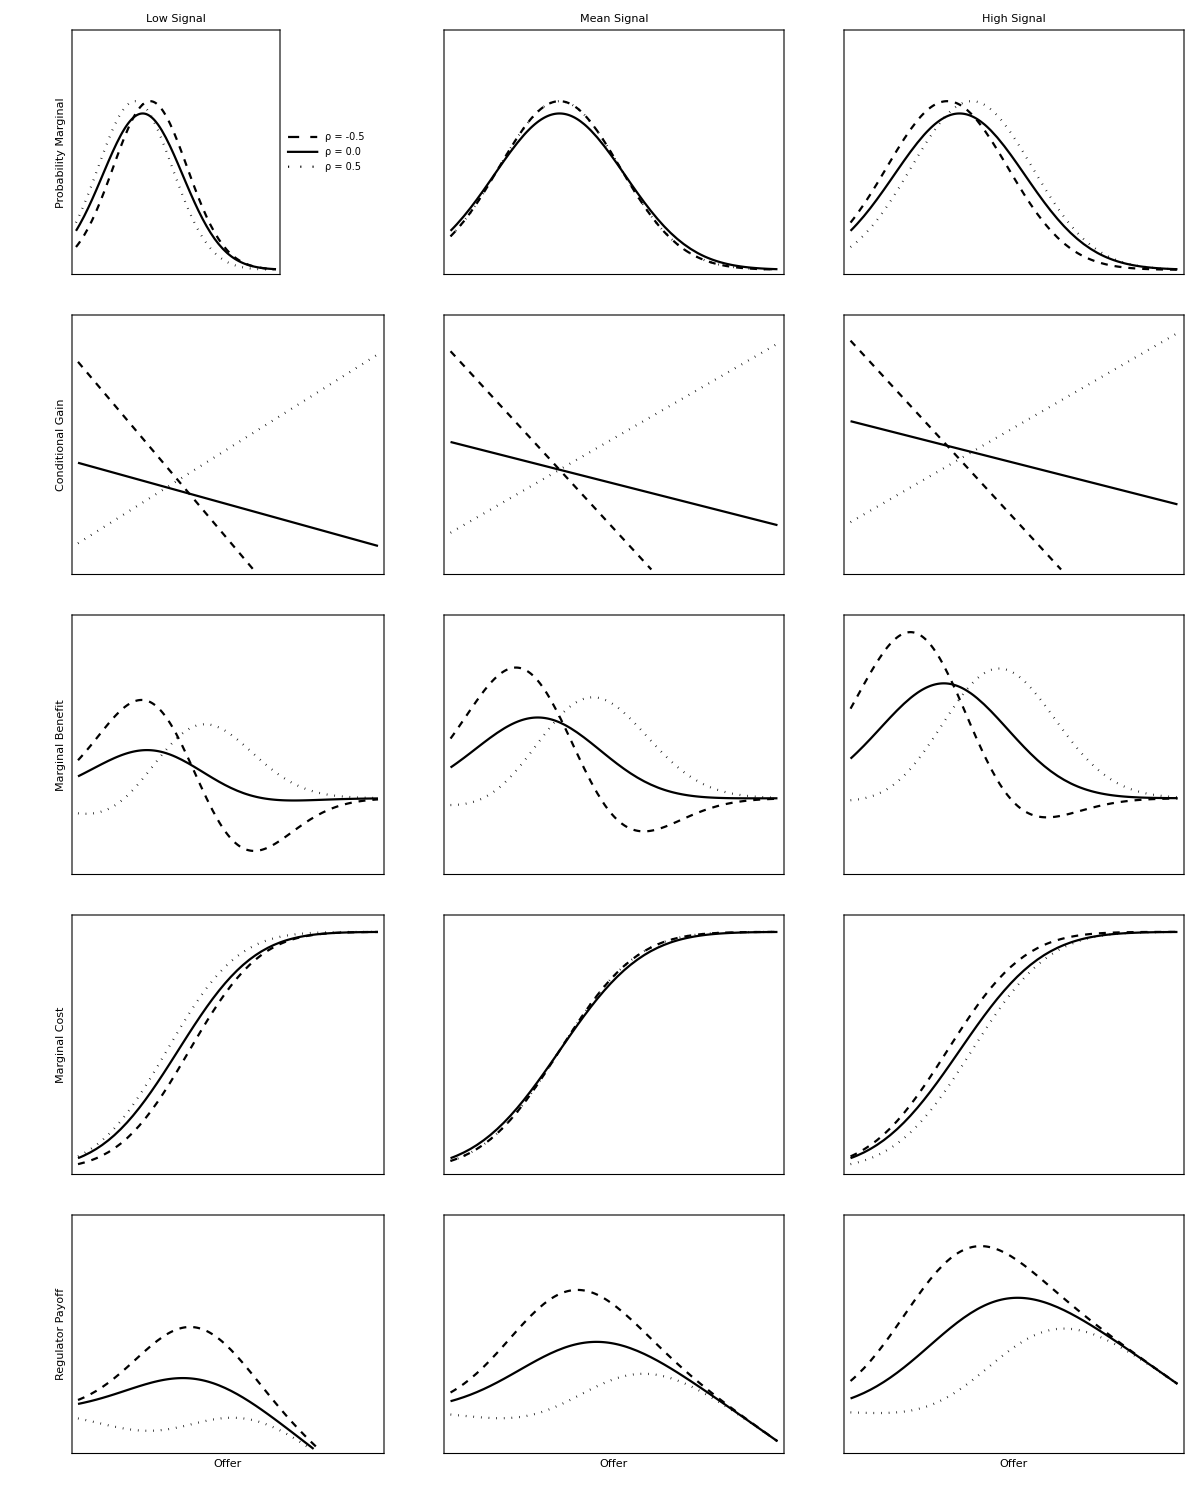

```mathematica
plotStyleList={{Black,Dashed},{Black},{Black,Dotted}};  baseSEnv = 1.5; baseMeanE = 1.3;
baseRhoES =.5;rhoEPVals = {-.75,0,.75}; rhoSPVals=rhoEPVals*baseRhoES;
plotOptionsMC = {PlotStyle->plotStyleList,PlotRange->{0,1.05},Ticks->None,Frame->{True,True,False,False},Axes->{True,True},LabelStyle->Black,FrameTicks->None};
plotOptionsPM = {PlotStyle->plotStyleList,PlotRange->{0,2},Ticks->None,Frame->{True,True,False,False},Axes->{True,True},LabelStyle->Black,FrameTicks->None};
plotOptionsCG = {PlotStyle->plotStyleList,PlotRange->{-1,3.5},Ticks->None,Frame->{False,True,False,False},Axes->{True,True},LabelStyle->Black,FrameTicks->None};
plotOptionsMB = {PlotStyle->plotStyleList,PlotRange->{-1,2.5},Ticks->None,Frame->{False,True,False,False},Axes->{True,True},LabelStyle->Black,FrameTicks->None};
plotOptionsRP = {PlotStyle->plotStyleList,PlotRange->{-.25,1.25},Ticks->None,Frame->{True,True,False,False},Axes->{True,True},LabelStyle->Black,FrameStyle->{White,{Thin,Black},White,White},FrameTicks->None};
plotGrid =Legended[
Grid[{
{Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsPM ,PlotLabel->"Low Signal",FrameLabel->{"","Probability Marginal"}],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsPM,PlotLabel->"Mean Signal",FrameLabel->{"",""}],
Plot[{
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pM[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsPM,PlotLabel->"High Signal",FrameLabel->{"",""}]},
{Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsCG,FrameLabel->{"","Conditional Gain"}],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsCG,FrameLabel->{"",""}],
Plot[{
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
condGain[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsCG,FrameLabel->{"",""}]},
{Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsMB,FrameLabel->{"","Marginal Benefit"}],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsMB,FrameLabel->{"",""}],
Plot[{
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
MB[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsMB,FrameLabel->{"",""}]},
{Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsMC,FrameLabel->{"","Marginal Cost"}],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsMC,FrameLabel->{"",""}],
Plot[{
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
pA[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsMC,FrameLabel->{"",""}]},
{Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsRP,FrameLabel->{Style["Offer",Black],"Regulator Payoff"}],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsRP,FrameLabel->{Style["Offer",Black],""}],
Plot[{
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
rpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsRP,FrameLabel->{Style["Offer",Black],""}]}
}],
Placed[LineLegend[{{Black,Dashed},Black,{Black,Dotted}},{"ρ = -0.5","ρ = 0.0","ρ = 0.5"},LegendLayout->"Row"],Below]]
Export["C:\\Users\\ssayre\\Documents\\activeProjectRepositories\\esvcsV2\\text\\plotGrid.eps",plotGrid,"EPS"];
```

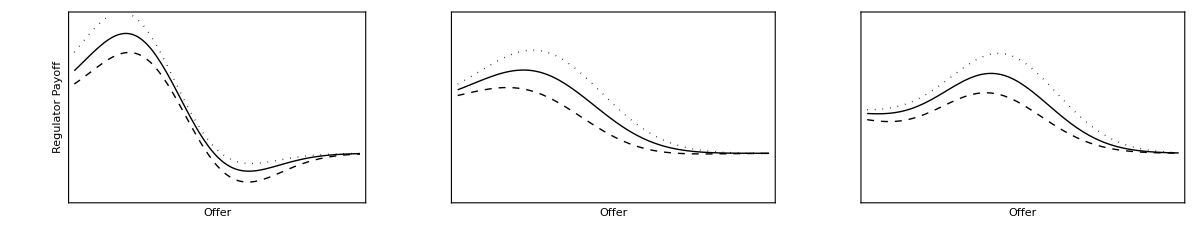

```mathematica
baseSEnv = 1.5; baseMeanE = 1.3;
baseRhoES =.5;rhoEPVals = {-.75,0,.75}; rhoSPVals=rhoEPVals*baseRhoES;
plotOptionsDRP = {PlotStyle->{{Thin,Black,Dashed},{Thin,Black},{Thin,Black,Dotted}},PlotRange->{-2,2},Ticks->None,Frame->{False,True,False,False},Axes->{True,True},FrameTicks->None};
GraphicsRow[{Plot[{
drpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
drpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]],
drpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[1]],rhoSPVals[[1]]]},
{x,0,xMax},Evaluate@plotOptionsDRP,FrameLabel->{"Offer","Regulator Payoff"}],
Plot[{
drpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
drpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]],
drpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[2]],rhoSPVals[[2]]]},
{x,0,xMax},Evaluate@plotOptionsDRP,FrameLabel->{"Offer",""}],
Plot[{
drpf[x,baseMeanE,baseMeanP,sigZVals[[1]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
drpf[x,baseMeanE,baseMeanP,sigZVals[[2]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]],
drpf[x,baseMeanE,baseMeanP,sigZVals[[3]],baseRhoES,baseSEnv,baseSrp,rhoEPVals[[3]],rhoSPVals[[3]]]},
{x,0,xMax},Evaluate@plotOptionsDRP,FrameLabel->{"Offer",""}]}]
```

```mathematica
Manipulate[Plot[{MB[x,meanE,meanP,s,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv]-pA[x,meanE,meanP,s,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv],MB[x,meanE,meanP,s+ds,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv]-pA[x,meanE,meanP,s+ds,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv]},{x,0,xMax},PlotRange-> {yMin,yMax},PlotLegends-> {"dR(s)","dR(s+ds)"}],
{{meanE,1,"μ_e"},0,4,.05,Appearance->Labeled},
{{meanP,1,"μ_p"},0,4,.05,Appearance->Labeled},
{{rhoESv,.5,"ρ_es"},0,1,.05,Appearance->Labeled},
{{s,0,"s"},-5,5,.05,Appearance->Labeled},
{{ds,.1,"ds"},0,.5,Appearance->Labeled},
{{sigE,1,"σ_e"},0,4,.05,Appearance->Labeled},
{{sigPv,1,"σ_p"},0,4,.05,Appearance->Labeled},
{{rhoEPv,.5,"ρ_ep"},0,1,.05,Appearance->Labeled},
{{xMax,2,"maxOffer"},.5,10,.1,Appearance->Labeled},
{{yMin,-1,"yMin"},-10,-.1,.1,Appearance->Labeled},
{{yMax,1,"yMax"},.1,10,.1,Appearance->Labeled}]
```

```mathematica
Manipulate[Plot[{MB[x,meanE,meanP,s,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv]-pA[x,meanE,meanP,s,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv],MB[x,meanE,meanP,s+ds,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv]-pA[x,meanE,meanP,s+ds,rhoESv,sigE,sigPv,rhoEPv,rhoEPv*rhoESv]},{x,0,xMax},PlotRange-> {yMin,yMax},PlotLegends-> {"dR(s)","dR(s+ds)"}],
{{meanE,1,"μ_e"},0,4,.05,Appearance->Labeled},
{{meanP,1,"μ_p"},0,4,.05,Appearance->Labeled},
{{rhoESv,.5,"ρ_es"},0,1,.05,Appearance->Labeled},
{{s,0,"s"},-5,5,.05,Appearance->Labeled},
{{ds,.1,"ds"},0,.5,Appearance->Labeled},
{{sigE,1,"σ_e"},0,4,.05,Appearance->Labeled},
{{sigPv,1,"σ_p"},0,4,.05,Appearance->Labeled},
{{rhoEPv,.5,"ρ_ep"},0,1,.05,Appearance->Labeled},
{{xMax,2,"maxOffer"},.5,10,.1,Appearance->Labeled},
{{yMin,-1,"yMin"},-10,-.1,.1,Appearance->Labeled},
{{yMax,1,"yMax"},.1,10,.1,Appearance->Labeled}]
```

```mathematica
Limit[MB[x,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],Subscript[ρ, ep],Subscript[ρ, ep]*Subscript[ρ, es]]-pA[x,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],Subscript[ρ, ep],Subscript[ρ, ep]*Subscript[ρ, es]],s->Infinity,Assumptions->{Subscript[ρ, ep]>0,Subscript[ρ, es]>0,Subscript[ρ, ep]<1,Subscript[ρ, es]<1,Subscript[σ, e]>0,Subscript[σ, p]>0}]
```

0

```mathematica
Limit[MB[x,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],0,0]-pA[x,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],0,0],s->Infinity,Assumptions->{Subscript[ρ, es]>0,Subscript[ρ, es]<1,Subscript[σ, e]>0,Subscript[σ, p]>0,x>=0,Subscript[μ, p]>0}]
```

∞

```mathematica
Limit[drpf[x,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],Subscript[ρ, ep],Subscript[ρ, ep]*Subscript[ρ, es]],x->-Infinity,Assumptions->{Subscript[ρ, ep]<1,Subscript[ρ, es]>0,Subscript[ρ, ep]>-1,Subscript[ρ, es]<1,Subscript[σ, e]>0,Subscript[σ, p]>0}]
```

0

```mathematica
Limit[drpf[x,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],Subscript[ρ, ep],Subscript[ρ, ep]*Subscript[ρ, es]],x->Infinity]
```

$Aborted

```mathematica
rpf[s*Subscript[ρ, ep]*Subscript[ρ, es]*Subscript[σ, p]+Subscript[μ, p]+extra,Subscript[μ, e],Subscript[μ, p],s,Subscript[ρ, es],Subscript[σ, e],Subscript[σ, p],Subscript[ρ, ep],Subscript[ρ, ep]*Subscript[ρ, es]],s->Infinity,Assumptions->{Subscript[ρ, ep]>0,Subscript[ρ, es]>=0,Subscript[ρ, ep]<=1,Subscript[ρ, es]<=1,Subscript[σ, e]>Subscript[σ, p],Subscript[σ, p]>0}]
```

∞ ρ_es erfc(-extra/(σ_p √(2-2 ρ_ep^2 ρ_es^2)))

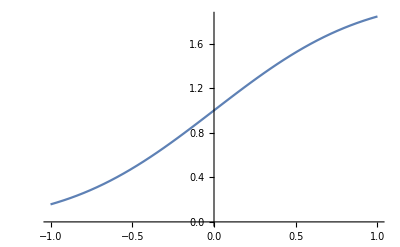

```mathematica
Plot[Erfc[-x],{x,-1 ,1}]
```

```mathematica
myGamma[rhoES_,rhoEP_]:=(1-rhoES^2)/(1-rhoES^2*rhoEP^2)
```

```mathematica
gamVal = myGamma[Subscript[ρ, es],Subscript[ρ, ep]]
```

(1-ρ_es^2)/(1-ρ_ep^2 ρ_es^2)

```mathematica
Limit[(Subscript[σ, e]*Subscript[ρ, es]*(1-gamVal*Subscript[ρ, ep]^2)*s+Subscript[μ, e]-Subscript[σ, e]*Subscript[ρ, ep]/Subscript[σ, p]*gamVal*Subscript[μ, p])/(1-gamVal*Subscript[σ, e]*Subscript[ρ, ep]/Subscript[σ, p]),s->Infinity,Assumptions->{Subscript[ρ, ep]>0,Subscript[ρ, es]>=0,Subscript[ρ, ep]<1,Subscript[ρ, es]<1,Subscript[σ, e]>Subscript[σ, p],Subscript[σ, p]>0,(1-gamVal*Subscript[σ, e]*Subscript[ρ, ep]/Subscript[σ, p])>0}]
```

∞ ρ_es

```mathematica
Limit[-b*x^2+c*x+d,x-> Infinity]
```

b (-∞)

```mathematica
Limit[(p[s]-h*s-muP)*h*(aval*p[s]+b*s+c)+sig2*(b-h),s-> Infinity]
```

lim_(s→∞) (h (-h s-μ_p+p(s)) (aval p(s)+b s+c)+sig2 (b-h))